```mathematica
M= 64*10^-6;
S= 10^-10;
 L= 1.1*10^-3;
  
G= 1.16*10^-5;
 r= 79; 
g= 10.75;
mpl= 2.44*10^18;
Clear[n]
n=(112*2*M/(3*1.2))NIntegrate[(epsi^2(1-E^{NIntegrate[(-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2),{T,0,1000},MaxRecursion->100, PrecisionGoal->3]})),{epsi,0,1000},MaxRecursion->100, PrecisionGoal->3]
Wh=n/(1.05*10^-5)
```

NIntegrate::inumr: The integrand -(1.96258×10^-12 epsi T^2)/(1/2441406250000000000+(0.000064-«22» T^3+1.06302×10^-8 T^5)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1.32681×10^6}

{1.26362×10^11}

```mathematica
Integrate[x^5+ x^3 + x^9, {x,0,4}]
```

1584064/15

```mathematica
1584064/15
```

1584064/15

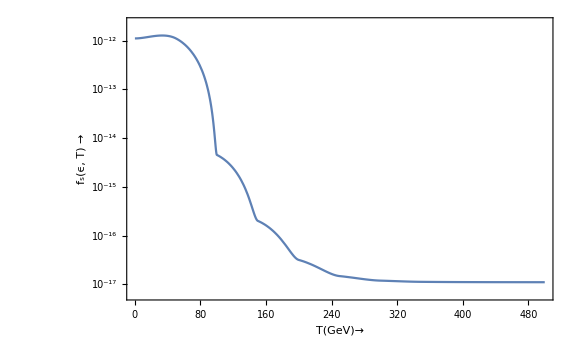

```mathematica
Parameters={M-> 64*10^-6(*GeV*) , S-> 10^-10, L-> 10^-4, epsi-> 0.0001 (*Scaled momentum(P/T)*), G-> 1.16*10^-5(*Fermi constant (GeV)*), r-> 79, g-> 61.75, mpl-> 2.44*10^18(*GeV*)};
solution = NDSolve[{ f'[T] ==((-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2))*(1/(E^epsi+1) - f[T]), f[10^6]== 0} /. Parameters, f , {T, 0,500}];
LogPlot[Evaluate[f[T]/. solution ]/.Parameters, {T,0,500},Frame-> True,FrameTicksStyle->Directive[Black,12],FrameLabel->{"T(GeV)→","f_s(ϵ, T) →"},PlotLegends->"Distribution of SN with a fixed scaled momentum " ,PlotStyle->Automatic, LabelStyle->Directive[Black,Bold, Medium],ImageSize->Large]
```

```mathematica
^(M= 64*10^-6;
S= 10^-10;
 L= 1.1*10^-3;
  
G= 1.16*10^-5;
 r= 79; 
g= 10.75;
mpl= 2.44*10^18;
Integrate[(-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2),{T,0,1000}])
```

NIntegrate::inumr: The integrand -(1.96258×10^-12 epsi T^2)/(1/2441406250000000000+(0.000064-«22» T^3+1.06302×10^-8 T^5)^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Null^(Null^7 NIntegrate[-(1.27 G^2 epsi T^2 M^2 S (45/(4 3.14)^3)^0.5 mpl)/((g^0.5 4) (M^2 S+(M (1-S)^0.5-(2 2^0.5 1.2 G L T^3)/3.14^2+r G^2 T^5)^2)),{T,0,1000},MaxRecursion→100,PrecisionGoal→3])

```mathematica
M= 64*10^-6;
S= 10^-10;
 L= 1.1*10^-3;
  
G= 1.16*10^-5;
 r= 79; 
g= 10.75;
mpl= 2.44*10^18;
epsi={0.00000001,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35000000000000003,0.36,0.37,0.38,0.39,0.4,0.41000000000000003,0.42,0.43,0.44,0.45,0.46,0.47000000000000003,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.6900000000000001,0.7000000000000001,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.8200000000000001,0.8300000000000001,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.9400000000000001,0.9500000000000001,0.96,0.97,0.98,0.99,1.0,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.1300000000000001,1.1400000000000001,1.1500000000000001,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.3800000000000001,1.3900000000000001,1.4000000000000001,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.6300000000000001,1.6400000000000001,1.6500000000000001,1.6600000000000001,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.8800000000000001,1.8900000000000001,1.9000000000000001,1.9100000000000001,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.0,2.0100000000000002,2.02,2.0300000000000002,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.2600000000000002,2.27,2.2800000000000002,2.29,2.3000000000000003,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.5100000000000002,2.52,2.5300000000000002,2.54,2.5500000000000003,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.7600000000000002,2.77,2.7800000000000002,2.79,2.8000000000000003,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.0,3.0100000000000002,3.02,3.0300000000000002,3.04,3.0500000000000003,3.06,3.0700000000000003,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.2600000000000002,3.27,3.2800000000000002,3.29,3.3000000000000003,3.31,3.3200000000000003,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.5100000000000002,3.52,3.5300000000000002,3.54,3.5500000000000003,3.56,3.5700000000000003,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.7600000000000002,3.77,3.7800000000000002,3.79,3.8000000000000003,3.81,3.8200000000000003,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.0,4.01,4.0200000000000005,4.03,4.04,4.05,4.0600000000000005,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.2700000000000005,4.28,4.29,4.3,4.3100000000000005,4.32,4.33,4.34,4.3500000000000005,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.5200000000000005,4.53,4.54,4.55,4.5600000000000005,4.57,4.58,4.59,4.6000000000000005,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.7700000000000005,4.78,4.79,4.8,4.8100000000000005,4.82,4.83,4.84,4.8500000000000005,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5.0,5.01,5.0200000000000005,5.03,5.04,5.05,5.0600000000000005,5.07,5.08,5.09,5.1000000000000005,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.2700000000000005,5.28,5.29,5.3,5.3100000000000005,5.32,5.33,5.34,5.3500000000000005,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.5200000000000005,5.53,5.54,5.55,5.5600000000000005,5.57,5.58,5.59,5.6000000000000005,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.7700000000000005,5.78,5.79,5.8,5.8100000000000005,5.82,5.83,5.84,5.8500000000000005,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.0,6.01,6.0200000000000005,6.03,6.04,6.05,6.0600000000000005,6.07,6.08,6.09,6.1000000000000005,6.11,6.12,6.13,6.140000000000001,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.2700000000000005,6.28,6.29,6.3,6.3100000000000005,6.32,6.33,6.34,6.3500000000000005,6.36,6.37,6.38,6.390000000000001,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.5200000000000005,6.53,6.54,6.55,6.5600000000000005,6.57,6.58,6.59,6.6000000000000005,6.61,6.62,6.63,6.640000000000001,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.7700000000000005,6.78,6.79,6.8,6.8100000000000005,6.82,6.83,6.84,6.8500000000000005,6.86,6.87,6.88,6.890000000000001,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7.0,7.01,7.0200000000000005,7.03,7.04,7.05,7.0600000000000005,7.07,7.08,7.09,7.1000000000000005,7.11,7.12,7.13,7.140000000000001,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.2700000000000005,7.28,7.29,7.3,7.3100000000000005,7.32,7.33,7.34,7.3500000000000005,7.36,7.37,7.38,7.390000000000001,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.5200000000000005,7.53,7.54,7.55,7.5600000000000005,7.57,7.58,7.59,7.6000000000000005,7.61,7.62,7.63,7.640000000000001,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.7700000000000005,7.78,7.79,7.8,7.8100000000000005,7.82,7.83,7.84,7.8500000000000005,7.86,7.87,7.88,7.890000000000001,7.9,7.91,7.92,7.930000000000001,7.94,7.95,7.96,7.97,7.98,7.99,8.0,8.01,8.02,8.03,8.040000000000001,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.120000000000001,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.290000000000001,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.370000000000001,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.540000000000001,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.620000000000001,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.700000000000001,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.790000000000001,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.870000000000001,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.950000000000001,8.96,8.97,8.98,8.99,9.0,9.01,9.02,9.03,9.040000000000001,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.120000000000001,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.200000000000001,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.290000000000001,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.370000000000001,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.450000000000001,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.540000000000001,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.620000000000001,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.700000000000001,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.790000000000001,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.870000000000001,9.88,9.89,9.9,9.91,9.92,9.93,9.94,9.950000000000001,9.96,9.97,9.98,9.99};
f=(epsi^2/(E^epsi +1))(1-E^NIntegrate[(-1.27*G^2*epsi*T^2*M^2*S*(45/(4*3.14)^3)^0.5*g^-0.5*mpl/4)/(M^2*S +(M*(1-S)^0.5-(2*2^0.5*1.2*G*L*T^3/3.14^2)+r*G^2*T^5)^2),{T,0,1000000000000},MaxRecursion->1000, PrecisionGoal->5])
```

{1.1826×10^-26,1.17655×10^-8,9.36401×10^-8,3.14402×10^-7,7.41381×10^-7,1.44045×10^-6,2.47606×10^-6,3.91118×10^-6,5.80737×10^-6,8.22474×10^-6,0.000011222,0.0000148563,0.0000191835,0.0000242581,0.0000301329,0.0000368596,0.0000444883,0.0000530678,0.0000626455,0.0000732673,0.0000849778,0.0000978202,0.000111836,0.000127067,0.000143551,0.000161326,0.000180429,0.000200895,0.000222758,0.000246049,0.000270802,0.000297044,0.000324806,0.000354114,0.000384995,0.000417474,0.000451573,0.000487317,0.000524725,0.000563818,0.000604615,0.000647134,0.000691391,0.000737401,0.000785179,0.000834738,0.000886089,0.000939245,0.000994214,0.00105101,0.00110963,0.00117009,0.00123239,0.00129654,0.00136254,0.00143039,0.0015001,0.00157167,0.00164509,0.00172037,0.0017975,0.00187649,0.00195732,0.00203999,0.0021245,0.00221083,0.002299,0.00238898,0.00248076,0.00257435,0.00266972,0.00276687,0.00286578,0.00296645,0.00306886,0.003173,0.00327885,0.0033864,0.00349563,0.00360652,0.00371907,0.00383325,0.00394905,0.00406644,0.00418541,0.00430593,0.004428,0.00455159,0.00467667,0.00480323,0.00493124,0.00506069,0.00519155,0.0053238,0.00545741,0.00559236,0.00572863,0.00586619,0.00600502,0.0061451,0.00628639,0.00642887,0.00657253,0.00671732,0.00686324,0.00701024,0.0071583,0.0073074,0.00745751,0.0076086,0.00776065,0.00791362,0.0080675,0.00822225,0.00837784,0.00853425,0.00869145,0.00884941,0.0090081,0.0091675,0.00932758,0.00948831,0.00964966,0.0098116,0.0099741,0.0101371,0.0103007,0.0104647,0.0106292,0.0107941,0.0109594,0.0111251,0.0112911,0.0114575,0.0116241,0.011791,0.0119581,0.0121254,0.0122929,0.0124605,0.0126283,0.0127962,0.0129641,0.0131321,0.0133001,0.013468,0.013636,0.0138039,0.0139717,0.0141394,0.014307,0.0144744,0.0146416,0.0148086,0.0149754,0.0151419,0.0153081,0.0154741,0.0156397,0.0158049,0.0159698,0.0161343,0.0162983,0.016462,0.0166251,0.0167878,0.01695,0.0171116,0.0172727,0.0174333,0.0175932,0.0177525,0.0179113,0.0180693,0.0182267,0.0183834,0.0185395,0.0186947,0.0188493,0.0190031,0.0191561,0.0193084,0.0194598,0.0196104,0.0197601,0.019909,0.0200571,0.0202042,0.0203505,0.0204958,0.0206402,0.0207837,0.0209261,0.0210677,0.0212082,0.0213477,0.0214863,0.0216238,0.0217602,0.0218957,0.02203,0.0221633,0.0222955,0.0224266,0.0225566,0.0226855,0.0228133,0.02294,0.0230655,0.0231898,0.023313,0.023435,0.0235559,0.0236756,0.023794,0.0239113,0.0240274,0.0241422,0.0242559,0.0243683,0.0244795,0.0245894,0.0246981,0.0248056,0.0249118,0.0250167,0.0251204,0.0252228,0.025324,0.0254238,0.0255224,0.0256197,0.0257157,0.0258104,0.0259039,0.025996,0.0260869,0.0261764,0.0262646,0.0263516,0.0264372,0.0265216,0.0266046,0.0266863,0.0267667,0.0268458,0.0269236,0.0270001,0.0270753,0.0271491,0.0272217,0.0272929,0.0273629,0.0274315,0.0274989,0.0275649,0.0276296,0.0276931,0.0277552,0.027816,0.0278756,0.0279338,0.0279908,0.0280465,0.0281008,0.0281539,0.0282058,0.0282563,0.0283056,0.0283536,0.0284004,0.0284459,0.0284901,0.0285331,0.0285748,0.0286153,0.0286545,0.0286925,0.0287293,0.0287648,0.0287992,0.0288323,0.0288642,0.0288948,0.0289243,0.0289526,0.0289797,0.0290056,0.0290303,0.0290539,0.0290762,0.0290974,0.0291175,0.0291364,0.0291541,0.0291708,0.0291862,0.0292006,0.0292138,0.0292259,0.0292369,0.0292468,0.0292556,0.0292633,0.02927,0.0292755,0.02928,0.0292834,0.0292858,0.0292871,0.0292874,0.0292866,0.0292848,0.029282,0.0292782,0.0292734,0.0292675,0.0292607,0.0292529,0.0292441,0.0292344,0.0292237,0.029212,0.0291994,0.0291858,0.0291713,0.0291559,0.0291396,0.0291223,0.0291042,0.0290851,0.0290652,0.0290444,0.0290227,0.0290002,0.0289767,0.0289525,0.0289274,0.0289015,0.0288747,0.0288471,0.0288187,0.0287895,0.0287595,0.0287288,0.0286972,0.0286649,0.0286318,0.0285979,0.0285633,0.0285279,0.0284919,0.028455,0.0284175,0.0283793,0.0283403,0.0283007,0.0282603,0.0282193,0.0281776,0.0281353,0.0280923,0.0280486,0.0280043,0.0279593,0.0279137,0.0278675,0.0278207,0.0277733,0.0277253,0.0276767,0.0276275,0.0275777,0.0275273,0.0274764,0.027425,0.0273729,0.0273204,0.0272673,0.0272137,0.0271595,0.0271049,0.0270497,0.026994,0.0269379,0.0268813,0.0268241,0.0267666,0.0267085,0.02665,0.026591,0.0265316,0.0264718,0.0264115,0.0263508,0.0262897,0.0262282,0.0261662,0.0261039,0.0260412,0.0259781,0.0259146,0.0258507,0.0257865,0.0257219,0.025657,0.0255917,0.0255261,0.0254601,0.0253938,0.0253272,0.0252603,0.0251931,0.0251255,0.0250577,0.0249896,0.0249211,0.0248524,0.0247835,0.0247142,0.0246447,0.0245749,0.0245049,0.0244347,0.0243641,0.0242934,0.0242224,0.0241512,0.0240798,0.0240082,0.0239363,0.0238643,0.0237921,0.0237196,0.023647,0.0235742,0.0235012,0.023428,0.0233547,0.0232812,0.0232076,0.0231338,0.0230598,0.0229857,0.0229115,0.0228371,0.0227626,0.022688,0.0226133,0.0225384,0.0224635,0.0223884,0.0223132,0.0222379,0.0221626,0.0220871,0.0220116,0.021936,0.0218603,0.0217845,0.0217087,0.0216328,0.0215568,0.0214808,0.0214047,0.0213286,0.0212525,0.0211763,0.0211,0.0210237,0.0209475,0.0208711,0.0207948,0.0207184,0.020642,0.0205657,0.0204893,0.0204129,0.0203365,0.0202601,0.0201837,0.0201073,0.0200309,0.0199546,0.0198783,0.019802,0.0197257,0.0196494,0.0195732,0.019497,0.0194209,0.0193448,0.0192687,0.0191927,0.0191168,0.0190409,0.018965,0.0188892,0.0188135,0.0187378,0.0186622,0.0185867,0.0185113,0.0184359,0.0183606,0.0182853,0.0182102,0.0181351,0.0180602,0.0179853,0.0179105,0.0178358,0.0177612,0.0176867,0.0176123,0.017538,0.0174639,0.0173898,0.0173158,0.017242,0.0171682,0.0170946,0.0170211,0.0169477,0.0168745,0.0168013,0.0167283,0.0166554,0.0165827,0.01651,0.0164376,0.0163652,0.016293,0.0162209,0.016149,0.0160772,0.0160055,0.015934,0.0158627,0.0157915,0.0157204,0.0156495,0.0155788,0.0155082,0.0154377,0.0153674,0.0152973,0.0152274,0.0151576,0.0150879,0.0150184,0.0149491,0.01488,0.014811,0.0147422,0.0146736,0.0146051,0.0145368,0.0144687,0.0144008,0.014333,0.0142654,0.014198,0.0141308,0.0140637,0.0139969,0.0139302,0.0138637,0.0137974,0.0137312,0.0136653,0.0135995,0.0135339,0.0134686,0.0134034,0.0133384,0.0132735,0.0132089,0.0131445,0.0130802,0.0130162,0.0129524,0.0128887,0.0128252,0.012762,0.0126989,0.012636,0.0125734,0.0125109,0.0124486,0.0123865,0.0123247,0.012263,0.0122015,0.0121402,0.0120792,0.0120183,0.0119576,0.0118972,0.0118369,0.0117769,0.011717,0.0116574,0.0115979,0.0115387,0.0114797,0.0114208,0.0113622,0.0113038,0.0112456,0.0111876,0.0111298,0.0110722,0.0110148,0.0109577,0.0109007,0.010844,0.0107874,0.0107311,0.0106749,0.010619,0.0105633,0.0105078,0.0104525,0.0103974,0.0103425,0.0102879,0.0102334,0.0101791,0.0101251,0.0100713,0.0100176,0.00996422,0.00991101,0.00985801,0.00980522,0.00975263,0.00970026,0.00964809,0.00959613,0.00954438,0.00949284,0.00944151,0.00939038,0.00933946,0.00928875,0.00923824,0.00918795,0.00913786,0.00908797,0.0090383,0.00898883,0.00893956,0.0088905,0.00884165,0.008793,0.00874456,0.00869633,0.00864829,0.00860047,0.00855284,0.00850543,0.00845821,0.0084112,0.00836439,0.00831778,0.00827138,0.00822518,0.00817918,0.00813338,0.00808779,0.00804239,0.0079972,0.0079522,0.00790741,0.00786281,0.00781842,0.00777422,0.00773022,0.00768642,0.00764282,0.00759941,0.0075562,0.00751319,0.00747037,0.00742775,0.00738533,0.0073431,0.00730106,0.00725922,0.00721757,0.00717611,0.00713485,0.00709378,0.0070529,0.00701221,0.00697171,0.0069314,0.00689129,0.00685136,0.00681162,0.00677207,0.0067327,0.00669353,0.00665454,0.00661574,0.00657712,0.00653869,0.00650045,0.00646239,0.00642451,0.00638682,0.00634931,0.00631198,0.00627483,0.00623787,0.00620109,0.00616448,0.00612806,0.00609182,0.00605575,0.00601986,0.00598416,0.00594862,0.00591327,0.00587809,0.00584309,0.00580826,0.0057736,0.00573912,0.00570482,0.00567068,0.00563672,0.00560293,0.00556931,0.00553586,0.00550258,0.00546947,0.00543653,0.00540376,0.00537116,0.00533872,0.00530645,0.00527435,0.00524241,0.00521063,0.00517902,0.00514758,0.00511629,0.00508517,0.00505422,0.00502342,0.00499278,0.00496231,0.00493199,0.00490183,0.00487184,0.004842,0.00481231,0.00478279,0.00475342,0.0047242,0.00469514,0.00466624,0.00463749,0.00460889,0.00458044,0.00455215,0.00452401,0.00449602,0.00446818,0.00444049,0.00441294,0.00438555,0.00435831,0.00433121,0.00430426,0.00427745,0.0042508,0.00422428,0.00419791,0.00417169,0.0041456,0.00411967,0.00409387,0.00406821,0.0040427,0.00401732,0.00399209,0.00396699,0.00394204,0.00391722,0.00389254,0.00386799,0.00384358,0.00381931,0.00379517,0.00377117,0.0037473,0.00372357,0.00369997,0.00367649,0.00365316,0.00362995,0.00360687,0.00358393,0.00356111,0.00353842,0.00351586,0.00349343,0.00347112,0.00344894,0.00342689,0.00340496,0.00338316,0.00336148,0.00333993,0.0033185,0.00329719,0.003276,0.00325493,0.00323399,0.00321317,0.00319246,0.00317188,0.00315141,0.00313106,0.00311083,0.00309072,0.00307072,0.00305084,0.00303108,0.00301143,0.00299189,0.00297247,0.00295316,0.00293397,0.00291488,0.00289591,0.00287705,0.0028583,0.00283966,0.00282113,0.00280271,0.00278439,0.00276619,0.00274809,0.0027301,0.00271222,0.00269444,0.00267676,0.00265919,0.00264173,0.00262437,0.00260711,0.00258996,0.00257291,0.00255596,0.00253911,0.00252236,0.00250571,0.00248916,0.00247272,0.00245637,0.00244011,0.00242396,0.0024079,0.00239194,0.00237608,0.00236031,0.00234464,0.00232906,0.00231358,0.00229819,0.00228289,0.00226769,0.00225257,0.00223756,0.00222263,0.00220779,0.00219304,0.00217839,0.00216382,0.00214934,0.00213496,0.00212065,0.00210644,0.00209232,0.00207828,0.00206432,0.00205046,0.00203668,0.00202298,0.00200937,0.00199584,0.00198239,0.00196903,0.00195575,0.00194256,0.00192944,0.00191641,0.00190346,0.00189059,0.0018778,0.00186509,0.00185245,0.0018399,0.00182742,0.00181503,0.00180271,0.00179046,0.0017783,0.00176621,0.0017542,0.00174226,0.00173039,0.00171861,0.00170689,0.00169525,0.00168368,0.00167219,0.00166077,0.00164942,0.00163814,0.00162693,0.0016158,0.00160473,0.00159374,0.00158281,0.00157196,0.00156117,0.00155045,0.0015398,0.00152922,0.00151871,0.00150826,0.00149788,0.00148757,0.00147732,0.00146713,0.00145702,0.00144696,0.00143698,0.00142705,0.00141719,0.0014074,0.00139766,0.00138799,0.00137838,0.00136884,0.00135935,0.00134993,0.00134056,0.00133126,0.00132202,0.00131284,0.00130371,0.00129465,0.00128564,0.0012767,0.00126781,0.00125898,0.0012502,0.00124149,0.00123283,0.00122423,0.00121568,0.00120719,0.00119875,0.00119037,0.00118205,0.00117378,0.00116556,0.00115739,0.00114929,0.00114123,0.00113323,0.00112527,0.00111738,0.00110953,0.00110173,0.00109399,0.0010863,0.00107866,0.00107106,0.00106352,0.00105603,0.00104859,0.0010412,0.00103385,0.00102656,0.00101931,0.00101211,0.00100496,0.000997857,0.000990801,0.000983792,0.000976829,0.000969913,0.000963042}

```mathematica
1/15625
```

1/15625

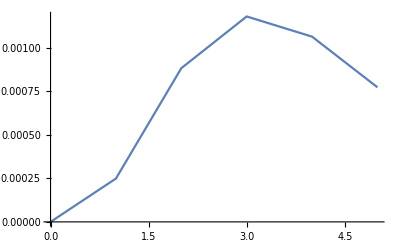

```mathematica
ListLinePlot[{   { 0.000001,    0},{ 1, 0.000249},{2,0.0008827},{3,0.00118},{4,0.001064},{5,0.000773}}]
```

```mathematica
M= 64*10^-6;
S= 10^-10;
 L= 1.1*10^-3;
  
G= 1.16*10^-5;
 r= 79; 
g= 10.75;
mpl= 2.44*10^18;
epsi={0.00000001,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35000000000000003,0.36,0.37,0.38,0.39,0.4,0.41000000000000003,0.42,0.43,0.44,0.45,0.46,0.47000000000000003,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.6900000000000001,0.7000000000000001,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.8200000000000001,0.8300000000000001,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.9400000000000001,0.9500000000000001,0.96,0.97,0.98,0.99,1.0,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.1300000000000001,1.1400000000000001,1.1500000000000001,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.3800000000000001,1.3900000000000001,1.4000000000000001,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.6300000000000001,1.6400000000000001,1.6500000000000001,1.6600000000000001,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.8800000000000001,1.8900000000000001,1.9000000000000001,1.9100000000000001,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.0,2.0100000000000002,2.02,2.0300000000000002,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.2600000000000002,2.27,2.2800000000000002,2.29,2.3000000000000003,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.5100000000000002,2.52,2.5300000000000002,2.54,2.5500000000000003,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.7600000000000002,2.77,2.7800000000000002,2.79,2.8000000000000003,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.0,3.0100000000000002,3.02,3.0300000000000002,3.04,3.0500000000000003,3.06,3.0700000000000003,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.2600000000000002,3.27,3.2800000000000002,3.29,3.3000000000000003,3.31,3.3200000000000003,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.5100000000000002,3.52,3.5300000000000002,3.54,3.5500000000000003,3.56,3.5700000000000003,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.7600000000000002,3.77,3.7800000000000002,3.79,3.8000000000000003,3.81,3.8200000000000003,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.0,4.01,4.0200000000000005,4.03,4.04,4.05,4.0600000000000005,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.2700000000000005,4.28,4.29,4.3,4.3100000000000005,4.32,4.33,4.34,4.3500000000000005,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.5200000000000005,4.53,4.54,4.55,4.5600000000000005,4.57,4.58,4.59,4.6000000000000005,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.7700000000000005,4.78,4.79,4.8,4.8100000000000005,4.82,4.83,4.84,4.8500000000000005,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5.0,5.01,5.0200000000000005,5.03,5.04,5.05,5.0600000000000005,5.07,5.08,5.09,5.1000000000000005,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.2700000000000005,5.28,5.29,5.3,5.3100000000000005,5.32,5.33,5.34,5.3500000000000005,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.5200000000000005,5.53,5.54,5.55,5.5600000000000005,5.57,5.58,5.59,5.6000000000000005,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.7700000000000005,5.78,5.79,5.8,5.8100000000000005,5.82,5.83,5.84,5.8500000000000005,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.0,6.01,6.0200000000000005,6.03,6.04,6.05,6.0600000000000005,6.07,6.08,6.09,6.1000000000000005,6.11,6.12,6.13,6.140000000000001,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.2700000000000005,6.28,6.29,6.3,6.3100000000000005,6.32,6.33,6.34,6.3500000000000005,6.36,6.37,6.38,6.390000000000001,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.5200000000000005,6.53,6.54,6.55,6.5600000000000005,6.57,6.58,6.59,6.6000000000000005,6.61,6.62,6.63,6.640000000000001,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.7700000000000005,6.78,6.79,6.8,6.8100000000000005,6.82,6.83,6.84,6.8500000000000005,6.86,6.87,6.88,6.890000000000001,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7.0,7.01,7.0200000000000005,7.03,7.04,7.05,7.0600000000000005,7.07,7.08,7.09,7.1000000000000005,7.11,7.12,7.13,7.140000000000001,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.2700000000000005,7.28,7.29,7.3,7.3100000000000005,7.32,7.33,7.34,7.3500000000000005,7.36,7.37,7.38,7.390000000000001,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.5200000000000005,7.53,7.54,7.55,7.5600000000000005,7.57,7.58,7.59,7.6000000000000005,7.61,7.62,7.63,7.640000000000001,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.7700000000000005,7.78,7.79,7.8,7.8100000000000005,7.82,7.83,7.84,7.8500000000000005,7.86,7.87,7.88,7.890000000000001,7.9,7.91,7.92,7.930000000000001,7.94,7.95,7.96,7.97,7.98,7.99,8.0,8.01,8.02,8.03,8.040000000000001,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.120000000000001,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.290000000000001,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.370000000000001,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.540000000000001,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.620000000000001,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.700000000000001,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.790000000000001,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.870000000000001,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.950000000000001,8.96,8.97,8.98,8.99,9.0,9.01,9.02,9.03,9.040000000000001,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.120000000000001,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.200000000000001,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.290000000000001,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.370000000000001,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.450000000000001,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.540000000000001,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.620000000000001,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.700000000000001,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.790000000000001,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.870000000000001,9.88,9.89,9.9,9.91,9.92,9.93,9.94,9.950000000000001,9.96,9.97,9.98,9.99};
f=(epsi^2/(E^epsi +1))
```

{5.×10^-17,0.00004975,0.000198,0.000443251,0.000784002,0.00121876,0.00174602,0.00236428,0.00307207,0.00386787,0.00475021,0.00571759,0.00676852,0.00790152,0.00911512,0.0104078,0.0117782,0.0132247,0.0147459,0.0163404,0.0180066,0.0197432,0.0215487,0.0234216,0.0253605,0.027364,0.0294306,0.0315589,0.0337476,0.0359951,0.0383002,0.0406613,0.0430772,0.0455464,0.0480676,0.0506393,0.0532604,0.0559293,0.0586447,0.0614054,0.06421,0.0670571,0.0699456,0.072874,0.0758411,0.0788456,0.0818862,0.0849617,0.0880709,0.0912124,0.0943852,0.0975878,0.100819,0.104078,0.107363,0.110674,0.114008,0.117366,0.120745,0.124145,0.127564,0.131001,0.134456,0.137927,0.141413,0.144913,0.148426,0.151951,0.155487,0.159033,0.162588,0.166151,0.169721,0.173296,0.176877,0.180462,0.18405,0.18764,0.191232,0.194824,0.198416,0.202007,0.205595,0.209181,0.212763,0.21634,0.219912,0.223478,0.227037,0.230588,0.234131,0.237665,0.241188,0.244702,0.248204,0.251694,0.255171,0.258635,0.262085,0.265521,0.268941,0.272346,0.275735,0.279106,0.28246,0.285796,0.289113,0.292411,0.295689,0.298948,0.302185,0.305402,0.308597,0.311769,0.31492,0.318047,0.321151,0.324231,0.327287,0.330318,0.333324,0.336305,0.339261,0.34219,0.345093,0.347969,0.350818,0.35364,0.356434,0.359201,0.361939,0.364649,0.36733,0.369982,0.372605,0.375199,0.377763,0.380297,0.382802,0.385276,0.38772,0.390133,0.392516,0.394867,0.397188,0.399478,0.401737,0.403964,0.40616,0.408325,0.410457,0.412559,0.414628,0.416665,0.418671,0.420645,0.422586,0.424496,0.426374,0.428219,0.430033,0.431814,0.433564,0.435281,0.436966,0.438619,0.44024,0.441829,0.443386,0.444911,0.446405,0.447866,0.449296,0.450694,0.45206,0.453395,0.454698,0.45597,0.45721,0.458419,0.459597,0.460745,0.461861,0.462946,0.464001,0.465025,0.466019,0.466982,0.467915,0.468818,0.469692,0.470535,0.471349,0.472133,0.472888,0.473614,0.474311,0.474979,0.475618,0.476229,0.476812,0.477366,0.477892,0.478391,0.478862,0.479305,0.479721,0.48011,0.480473,0.480808,0.481117,0.4814,0.481656,0.481887,0.482092,0.482271,0.482425,0.482554,0.482658,0.482738,0.482792,0.482823,0.482829,0.482812,0.482771,0.482707,0.482619,0.482508,0.482375,0.482219,0.48204,0.48184,0.481617,0.481373,0.481108,0.480821,0.480513,0.480184,0.479835,0.479465,0.479075,0.478665,0.478235,0.477786,0.477317,0.47683,0.476323,0.475798,0.475255,0.474693,0.474114,0.473516,0.472901,0.472269,0.47162,0.470953,0.47027,0.469571,0.468855,0.468123,0.467376,0.466613,0.465834,0.46504,0.464231,0.463408,0.46257,0.461717,0.460851,0.45997,0.459076,0.458168,0.457247,0.456312,0.455365,0.454405,0.453433,0.452448,0.451451,0.450442,0.449422,0.448389,0.447346,0.446291,0.445225,0.444149,0.443062,0.441964,0.440857,0.439739,0.438611,0.437474,0.436327,0.435171,0.434006,0.432832,0.431649,0.430457,0.429257,0.428049,0.426833,0.425609,0.424377,0.423137,0.42189,0.420636,0.419374,0.418106,0.416831,0.415549,0.414261,0.412966,0.411666,0.410359,0.409046,0.407728,0.406404,0.405075,0.403741,0.402401,0.401057,0.399708,0.398354,0.396995,0.395632,0.394265,0.392894,0.391519,0.39014,0.388757,0.38737,0.38598,0.384587,0.383191,0.381791,0.380388,0.378983,0.377575,0.376164,0.374751,0.373336,0.371918,0.370498,0.369076,0.367652,0.366226,0.364799,0.36337,0.36194,0.360508,0.359075,0.357641,0.356205,0.354769,0.353332,0.351894,0.350456,0.349017,0.347577,0.346137,0.344697,0.343257,0.341816,0.340376,0.338935,0.337495,0.336055,0.334615,0.333176,0.331737,0.330299,0.328861,0.327425,0.325989,0.324553,0.323119,0.321686,0.320254,0.318823,0.317394,0.315966,0.314539,0.313113,0.31169,0.310267,0.308847,0.307428,0.306011,0.304596,0.303182,0.301771,0.300362,0.298955,0.29755,0.296147,0.294746,0.293348,0.291952,0.290559,0.289168,0.287779,0.286394,0.28501,0.28363,0.282252,0.280877,0.279505,0.278135,0.276769,0.275405,0.274045,0.272688,0.271333,0.269982,0.268634,0.267289,0.265947,0.264609,0.263274,0.261942,0.260614,0.259289,0.257968,0.25665,0.255335,0.254024,0.252717,0.251413,0.250113,0.248817,0.247524,0.246235,0.24495,0.243669,0.242391,0.241117,0.239847,0.238581,0.237319,0.236061,0.234807,0.233556,0.23231,0.231068,0.229829,0.228595,0.227365,0.226139,0.224917,0.223699,0.222486,0.221276,0.220071,0.21887,0.217673,0.21648,0.215291,0.214107,0.212927,0.211752,0.21058,0.209413,0.20825,0.207092,0.205937,0.204788,0.203642,0.202501,0.201364,0.200232,0.199104,0.19798,0.196861,0.195746,0.194636,0.19353,0.192428,0.191331,0.190238,0.18915,0.188066,0.186986,0.185911,0.184841,0.183774,0.182713,0.181655,0.180603,0.179554,0.17851,0.177471,0.176436,0.175405,0.174379,0.173358,0.17234,0.171328,0.170319,0.169316,0.168316,0.167321,0.166331,0.165345,0.164363,0.163386,0.162413,0.161445,0.160481,0.159521,0.158566,0.157615,0.156669,0.155727,0.15479,0.153857,0.152928,0.152003,0.151083,0.150168,0.149256,0.14835,0.147447,0.146549,0.145655,0.144765,0.14388,0.142999,0.142122,0.14125,0.140381,0.139517,0.138658,0.137802,0.136951,0.136104,0.135262,0.134423,0.133589,0.132759,0.131933,0.131111,0.130294,0.12948,0.128671,0.127866,0.127065,0.126268,0.125475,0.124687,0.123902,0.123122,0.122345,0.121573,0.120804,0.12004,0.11928,0.118523,0.117771,0.117023,0.116278,0.115538,0.114801,0.114069,0.11334,0.112615,0.111894,0.111177,0.110464,0.109755,0.109049,0.108348,0.10765,0.106956,0.106266,0.105579,0.104897,0.104218,0.103543,0.102871,0.102204,0.10154,0.100879,0.100222,0.0995695,0.0989201,0.0982743,0.0976322,0.0969937,0.0963587,0.0957274,0.0950996,0.0944753,0.0938546,0.0932374,0.0926237,0.0920135,0.0914068,0.0908035,0.0902037,0.0896074,0.0890144,0.0884249,0.0878388,0.087256,0.0866767,0.0861006,0.0855279,0.0849586,0.0843925,0.0838298,0.0832703,0.0827142,0.0821612,0.0816115,0.0810651,0.0805218,0.0799818,0.0794449,0.0789112,0.0783807,0.0778533,0.0773291,0.0768079,0.0762899,0.0757749,0.0752631,0.0747543,0.0742485,0.0737458,0.0732461,0.0727493,0.0722556,0.0717649,0.0712771,0.0707923,0.0703104,0.0698314,0.0693554,0.0688822,0.0684119,0.0679445,0.0674799,0.0670182,0.0665593,0.0661032,0.0656499,0.0651994,0.0647517,0.0643067,0.0638645,0.063425,0.0629882,0.0625541,0.0621227,0.061694,0.0612679,0.0608445,0.0604237,0.0600056,0.0595901,0.0591771,0.0587668,0.058359,0.0579538,0.0575511,0.0571509,0.0567533,0.0563582,0.0559655,0.0555754,0.0551877,0.0548025,0.0544197,0.0540393,0.0536614,0.0532858,0.0529127,0.0525419,0.0521735,0.0518074,0.0514437,0.0510823,0.0507232,0.0503664,0.0500119,0.0496597,0.0493097,0.0489621,0.0486166,0.0482734,0.0479324,0.0475936,0.0472569,0.0469225,0.0465902,0.0462601,0.0459322,0.0456063,0.0452826,0.044961,0.0446415,0.0443241,0.0440087,0.0436955,0.0433842,0.043075,0.0427679,0.0424627,0.0421596,0.0418584,0.0415592,0.0412621,0.0409668,0.0406735,0.0403822,0.0400927,0.0398052,0.0395196,0.0392359,0.0389541,0.0386741,0.038396,0.0381198,0.0378454,0.0375728,0.0373021,0.0370331,0.0367659,0.0365006,0.036237,0.0359752,0.0357151,0.0354568,0.0352002,0.0349453,0.0346922,0.0344407,0.034191,0.0339429,0.0336965,0.0334518,0.0332087,0.0329672,0.0327274,0.0324893,0.0322527,0.0320178,0.0317844,0.0315526,0.0313224,0.0310938,0.0308667,0.0306412,0.0304172,0.0301948,0.0299738,0.0297544,0.0295365,0.02932,0.0291051,0.0288916,0.0286796,0.0284691,0.0282599,0.0280523,0.027846,0.0276412,0.0274378,0.0272358,0.0270352,0.026836,0.0266381,0.0264416,0.0262465,0.0260528,0.0258603,0.0256692,0.0254795,0.025291,0.0251039,0.0249181,0.0247335,0.0245503,0.0243683,0.0241876,0.0240081,0.0238299,0.023653,0.0234773,0.0233028,0.0231295,0.0229575,0.0227866,0.022617,0.0224485,0.0222813,0.0221152,0.0219503,0.0217865,0.0216239,0.0214624,0.0213021,0.0211429,0.0209848,0.0208279,0.020672,0.0205173,0.0203636,0.020211,0.0200596,0.0199092,0.0197598,0.0196115,0.0194643,0.0193181,0.019173,0.0190289,0.0188858,0.0187437,0.0186027,0.0184626,0.0183236,0.0181855,0.0180485,0.0179124,0.0177773,0.0176431,0.0175099,0.0173777,0.0172464,0.0171161,0.0169867,0.0168582,0.0167306,0.016604,0.0164783,0.0163534,0.0162295,0.0161065,0.0159843,0.0158631,0.0157427,0.0156232,0.0155045,0.0153867,0.0152698,0.0151537,0.0150384,0.014924,0.0148104,0.0146976,0.0145856,0.0144745,0.0143642,0.0142546,0.0141459,0.0140379,0.0139308,0.0138244,0.0137188,0.013614,0.0135099,0.0134066,0.013304,0.0132022,0.0131011,0.0130008,0.0129012,0.0128023,0.0127042,0.0126068,0.0125101,0.0124141,0.0123188,0.0122242,0.0121303,0.0120371,0.0119445,0.0118527,0.0117615,0.011671,0.0115812,0.011492,0.0114035,0.0113156,0.0112284,0.0111418,0.0110559,0.0109706,0.0108859,0.0108019,0.0107185,0.0106357,0.0105535,0.0104719,0.0103909,0.0103105,0.0102308,0.0101516,0.010073,0.00999496,0.00991752,0.00984066,0.00976437,0.00968865,0.00961349,0.00953889,0.00946485,0.00939136,0.00931841,0.00924601,0.00917415,0.00910283,0.00903204,0.00896178,0.00889204,0.00882283,0.00875413,0.00868595,0.00861828,0.00855111,0.00848445,0.00841829,0.00835262,0.00828745,0.00822276,0.00815856,0.00809485,0.00803161,0.00796885,0.00790656,0.00784474,0.00778338,0.00772249,0.00766205,0.00760207,0.00754255,0.00748347,0.00742483,0.00736664,0.00730889,0.00725158,0.0071947,0.00713825,0.00708222,0.00702662,0.00697144,0.00691668,0.00686233,0.0068084,0.00675487,0.00670175,0.00664903,0.00659672,0.0065448,0.00649327,0.00644214,0.00639139,0.00634103,0.00629105,0.00624146,0.00619224,0.00614339,0.00609492,0.00604682,0.00599908,0.00595171,0.0059047,0.00585805,0.00581175,0.00576581,0.00572022,0.00567498,0.00563008,0.00558553,0.00554131,0.00549744,0.0054539,0.0054107,0.00536782,0.00532528,0.00528306,0.00524116,0.00519959,0.00515833,0.00511739,0.00507677,0.00503646,0.00499646,0.00495676,0.00491737,0.00487829,0.0048395,0.00480102,0.00476283,0.00472493,0.00468733,0.00465001,0.00461298,0.00457624}

```mathematica
Clear[x,M,S, L]
x={0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35000000000000003,0.36,0.37,0.38,0.39,0.4,0.41000000000000003,0.42,0.43,0.44,0.45,0.46,0.47000000000000003,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.6900000000000001,0.7000000000000001,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.8200000000000001,0.8300000000000001,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.9400000000000001,0.9500000000000001,0.96,0.97,0.98,0.99,1.0,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.1300000000000001,1.1400000000000001,1.1500000000000001,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.3800000000000001,1.3900000000000001,1.4000000000000001,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.6300000000000001,1.6400000000000001,1.6500000000000001,1.6600000000000001,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.8800000000000001,1.8900000000000001,1.9000000000000001,1.9100000000000001,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.0,2.0100000000000002,2.02,2.0300000000000002,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.2600000000000002,2.27,2.2800000000000002,2.29,2.3000000000000003,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.5100000000000002,2.52,2.5300000000000002,2.54,2.5500000000000003,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.7600000000000002,2.77,2.7800000000000002,2.79,2.8000000000000003,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.0,3.0100000000000002,3.02,3.0300000000000002,3.04,3.0500000000000003,3.06,3.0700000000000003,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.2600000000000002,3.27,3.2800000000000002,3.29,3.3000000000000003,3.31,3.3200000000000003,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.5100000000000002,3.52,3.5300000000000002,3.54,3.5500000000000003,3.56,3.5700000000000003,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.7600000000000002,3.77,3.7800000000000002,3.79,3.8000000000000003,3.81,3.8200000000000003,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.0,4.01,4.0200000000000005,4.03,4.04,4.05,4.0600000000000005,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.2700000000000005,4.28,4.29,4.3,4.3100000000000005,4.32,4.33,4.34,4.3500000000000005,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.5200000000000005,4.53,4.54,4.55,4.5600000000000005,4.57,4.58,4.59,4.6000000000000005,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.7700000000000005,4.78,4.79,4.8,4.8100000000000005,4.82,4.83,4.84,4.8500000000000005,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5.0,5.01,5.0200000000000005,5.03,5.04,5.05,5.0600000000000005,5.07,5.08,5.09,5.1000000000000005,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.2700000000000005,5.28,5.29,5.3,5.3100000000000005,5.32,5.33,5.34,5.3500000000000005,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.5200000000000005,5.53,5.54,5.55,5.5600000000000005,5.57,5.58,5.59,5.6000000000000005,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.7700000000000005,5.78,5.79,5.8,5.8100000000000005,5.82,5.83,5.84,5.8500000000000005,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.0,6.01,6.0200000000000005,6.03,6.04,6.05,6.0600000000000005,6.07,6.08,6.09,6.1000000000000005,6.11,6.12,6.13,6.140000000000001,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.2700000000000005,6.28,6.29,6.3,6.3100000000000005,6.32,6.33,6.34,6.3500000000000005,6.36,6.37,6.38,6.390000000000001,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.5200000000000005,6.53,6.54,6.55,6.5600000000000005,6.57,6.58,6.59,6.6000000000000005,6.61,6.62,6.63,6.640000000000001,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.7700000000000005,6.78,6.79,6.8,6.8100000000000005,6.82,6.83,6.84,6.8500000000000005,6.86,6.87,6.88,6.890000000000001,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7.0,7.01,7.0200000000000005,7.03,7.04,7.05,7.0600000000000005,7.07,7.08,7.09,7.1000000000000005,7.11,7.12,7.13,7.140000000000001,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.2700000000000005,7.28,7.29,7.3,7.3100000000000005,7.32,7.33,7.34,7.3500000000000005,7.36,7.37,7.38,7.390000000000001,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.5200000000000005,7.53,7.54,7.55,7.5600000000000005,7.57,7.58,7.59,7.6000000000000005,7.61,7.62,7.63,7.640000000000001,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.7700000000000005,7.78,7.79,7.8,7.8100000000000005,7.82,7.83,7.84,7.8500000000000005,7.86,7.87,7.88,7.890000000000001,7.9,7.91,7.92,7.930000000000001,7.94,7.95,7.96,7.97,7.98,7.99,8.0,8.01,8.02,8.03,8.040000000000001,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.120000000000001,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.290000000000001,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.370000000000001,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.540000000000001,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.620000000000001,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.700000000000001,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.790000000000001,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.870000000000001,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.950000000000001,8.96,8.97,8.98,8.99,9.0,9.01,9.02,9.03,9.040000000000001,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.120000000000001,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.200000000000001,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.290000000000001,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.370000000000001,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.450000000000001,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.540000000000001,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.620000000000001,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.700000000000001,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.790000000000001,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.870000000000001,9.88,9.89,9.9,9.91,9.92,9.93,9.94,9.950000000000001,9.96,9.97,9.98,9.99};M=2*10^-6;
S=10^-10;
L=6*10^-3;
g=61.75;
mpl= 2.44*10^19;

G= 1.16*10^-5;

f=(x^2/(1+E^x))(1-E^(NIntegrate[(M^4*S/(4*x^2 T^2))(-0.92*G^2*x *T^2*g^-0.5*mpl/4)/(M^4*S /(4*x^2 T^2)+(M^2/(2x T)-(2*2^0.5*1.2*G*L* T^3/3.14^2)+0.92*G^2*x T^5)^2),{T,0.1,1000},MaxRecursion->1000, PrecisionGoal->10]))
```

```mathematica
{8.653918803452048*^-8,7.396234990760553*^-7,2.6735463940559832*^-6,6.8058407381202875*^-6,0.000014316997076806895,0.00002672977393684633,0.000046015365272978117,0.00007473672396276297,0.00011624378605116561,0.0001749419191819912,0.0002566647446264143,0.00036919728102547626,0.0005230177892543008,0.0007323607947400462,0.001016755394259074,0.0014032698283353805,0.0019298027498600536,0.0026499002376826107,0.003639693708222952,0.005007422573319612,0.006904829230305661,0.00953489758183106,0.013134172651639908,0.017861214834246103,0.023434010495797117,0.02850801381864273,0.03154230875202515,0.03374757604294964,0.03599512522045928,0.03830017348695069,0.04066128022589645,0.042943506178136415,0.0437206943288772,0.042007381733433366,0.03884556840112378,0.03533290349788511,0.03201628280833679,0.029083204509902583,0.026558386008087825,0.0244058082387883,0.022572895698880976,0.02100769507820475,0.019664582864150675,0.018505389716095104,0.017498850439650264,0.016619565954220518,0.015846935848890475,0.015164218294137733,0.014557752911713727,0.014016337017273754,0.013530731807289146,0.013093273567181244,0.012697567829913589,0.01233824834032205,0.012010786431798651,0.011711339601344335,0.011436630621250467,0.011183850518944263,0.010950580291365268,0.01073472739407281,0.010534473940861516,0.010348234233150852,0.010174619761100161,0.010012410219372018,0.009860529389255464,0.009718024977687324,0.009584051689271633,0.009457856952259707,0.009338768833084538,0.009226185763605505,0.009119567776148092,0.009018428997856926,0.008922331200990839,0.00883087824200759,0.00874371125149484,0.008660504460660651,0.008580961569334631,0.008504812576139626,0.008431811004371036,0.00836173146771529,0.00829436752868955,0.0082295298099366,0.008167044324539054,0.008106750996550083,0.008048502347149822,0.007992162325373704,0.007937605265339423,0.007884714954414798,0.00783338379890177,0.007783512075623356,0.007735007259342038,0.007687783417257145,0.007641760662955585,0.0075968646631592255,0.0075530261914447385,0.007510180723829925,0.007468268071741558,0.007427232048416627,0.007387020165256254,0.0073475833550570415,0.007308875719397526,0.007270854297767658,0.007233478856297946,0.007196711694182652,0.0071605174660983855,0.0071248630191036244,0.007089717242664112,0.007055050930592741,0.007020836653817358,0.00698704864300156,0.0069536626801419065,0.006920655998353129,0.00688800718913033,0.006855696116446855,0.0068237038371083865,0.006792012526839227,0.00676060541162573,0.006729466703886891,0.006698581543081283,0.006667935940394867,0.00663751672718756,0.006607311506903437,0.006577308610177142,0.006547497052891479,0.006517866496962542,0.006488407213648235,0.006459110049192922,0.006429966392636597,0.006400968145632117,0.006372107694125109,0.006343377881765333,0.0063147719849265555,0.006286283689223443,0.006257907067421948,0.006229636558648441,0.006201466948808948,0.0061733933521384236,0.0061454111938044785,0.006117516193496532,0.006089704349936582,0.006061971926251589,0.006034315436153353,0.006006731630874123,0.005979217486811066,0.0059517701938357525,0.005924387144227232,0.00589706592219125,0.0058698042939304175,0.005842600198231608,0.0058154517375410275,0.005788357169497401,0.005761314898897166,0.005734323470066806,0.00570738155961853,0.005680487969568663,0.00565364162079677,0.005626841546828457,0.005600086887922315,0.0055733768854454606,0.005546710876521692,0.005520088288937289,0.0054935086362913705,0.005466971513377401,0.005440476591783503,0.0054140236157012075,0.005387612397930768,0.005361242816073383,0.0053349148089013865,0.005308628372896478,0.005282383558948124,0.005256180469204628,0.00523001925406823,0.00520390010932828,0.00517782327342527,0.005151789024839443,0.00512579767959823,0.005099849588896736,0.005073945136825867,0.005048084738203522,0.005022268836503239,0.0049964979018770166,0.0049707724292663005,0.004945092936599219,0.004919459963068143,0.004893874067485517,0.004868335826713457,0.0048428458341643445,0.004817404698369291,0.00479201304161123,0.004766671498620164,0.004741380715327312,0.0047161413476763964,0.004690954060489062,0.004665819526382333,0.0046407384247356,0.004615711440705692,0.004590739264287369,0.004565822589417557,0.004540962113121778,0.004516158534700428,0.004491412554953997,0.004466724875445078,0.0044420961977955755,0.004417527223018515,0.004393018650881833,0.004368571179304184,0.004344185503779876,0.004319862316833607,0.004295602307502129,0.004271406160843049,0.0042472745574684955,0.004223208173104041,0.004199207678170418,0.0041752737373882826,0.0041514070094045095,0.004127608146439301,0.004103877793953289,0.0040802165903337725,0.004056625166599767,0.004033104146124211,0.004009654144373731,0.003986275768664297,0.003962969617933089,0.0039397362825247815,0.003916576343993011,0.0038934903749152793,0.003870478938721523,0.0038475425895351306,0.003824681872026778,0.003801897321279572,0.003779189462665995,0.0037565588117355756,0.003734005874112897,0.0037115311454058437,0.003689135111123353,0.003666818246602483,0.003644581016944493,0.003622423876958839,0.0036003472711163193,0.0035783516335089107,0.003556437387818178,0.0035346049472899372,0.0035128547147163314,0.003491187082424485,0.0034696024322712275,0.0034481011356439443,0.0034266835534673273,0.003405350036215442,0.0033841009239293034,0.00336293654623921,0.003341857222392173,0.0033208632612839266,0.003299954961495012,0.0032791326113313667,0.0032583964888689533,0.0032377468620017383,0.00321718398849396,0.0031967081160352503,0.003176319482299378,0.0031560183150057494,0.003135804831984534,0.003115679241243771,0.0030956417410396846,0.0030756925199492977,0.0030558317569454327,0.0030360596214740725,0.0030163762735336283,0.0029967818637564344,0.002977276533491885,0.0029578604148914017,0.002938533630995316,0.002919296295820699,0.002900148514451315,0.0028810903831283908,0.0028621219893428854,0.0028432434119288587,0.0028244547211578063,0.002805755978834147,0.0027871472383914245,0.002768628544989555,0.002750199935612429,0.0027318614391666674,0.0027136130765805246,0.00269545486090357,0.0026773867974068484,0.0026594088836831686,0.0026415211097481784,0.002623723458141101,0.0026060159040263964,0.002588398415294993,0.002570870952665934,0.002553433469788177,0.0025360859133418834,0.0025188282231404418,0.0025016603322318763,0.0024845821670002304,0.002467593647266876,0.0024506946863917024,0.0024338851913738237,0.0024171650629522443,0.0024005341957061476,0.0023839924781547603,0.002367539792856934,0.0023511760165104674,0.002334901020050654,0.0023187146687485777,0.0023026168223091595,0.002286607334968195,0.0022706860555891362,0.0022548528277596333,0.002239107489886776,0.002223449875292296,0.002207879812307207,0.0021923971243653145,0.0021770016300964707,0.002161693143419237,0.002146471473632419,0.002131336425506383,0.0021162877993734525,0.0021013253912174697,0.002086448992762887,0.0020716583915628578,0.0020569533710867614,0.0020423337108068543,0.0020277991862842184,0.00201334956925382,0.001998984627708851,0.0019847041259842433,0.001970507824839489,0.0019563954815404764,0.0019423668499405093,0.0019284216805607452,0.0019145597206694802,0.0019007807143608068,0.0018870844026324621,0.0018734705234626729,0.0018599388118862139,0.0018464890000698005,0.0018331208173864358,0.0018198339904887792,0.0018066282433822918,0.001793503297496555,0.0017804588717568045,0.0017674946826537364,0.0017546104443129688,0.0017418058685635407,0.0017290806650054533,0.0017164345410765967,0.001703867202118558,0.0016913783514417098,0.00167896769038963,0.0016666349184023975,0.0016543797330792714,0.0016422018302403986,0.0016301009039877193,0.001618076646765207,0.0016061287494181036,0.0015942569012513425,0.001582460790087337,0.001570740102322726,0.0015590945229845157,0.001547523735785284,0.0015360274231777328,0.0015246052664081749,0.001513256945569707,0.001501982139653996,0.0014907805266029246,0.0014796517833589526,0.0014685955859150195,0.0014576116093634477,0.0014466995279444792,0.0014358590150936445,0.001425089743488563,0.0014143913850950401,0.0014037636112125271,0.0013932060925184652,0.0013827184991125085,0.0013723005005594326,0.0013619517659317893,0.0013516719638516138,0.0013414607625315063,0.001331317829815086,0.001321242833216691,0.0013112354399603618,0.0013012953170183465,0.0012914221311487344,0.0012816155489325767,0.0012718752368102164,0.0012622008611171427,0.001252592088119163,0.0012430485840467674,0.001233570015129283,0.0012241560476278256,0.001214806347868245,0.0012055205822730365,0.001196298417392881,0.0011871395199374584,0.0011780435568059125,0.0011690101951163055,0.0011600391022350478,0.0011511299458053456,0.0011422823937752415,0.0011334961144250936,0.0011247707763946326,0.0011161060487092467,0.001107501600805902,0.0010989571025584466,0.0010904722243025463,0.0010820466368599369,0.001073680011562251,0.0010653720202743642,0.0010571223354171675,0.0010489306299900022,0.0010407965775923952,0.0010327198524455478,0.0010247001294132379,0.0010167370840222859,0.001008830392482465,0.0010009797317061793,0.0009931847793274856,0.0009854452137208185,0.0009777607140192318,0.0009701309601321611,0.0009625556327628702,0.0009550344134253536,0.0009475669844610549,0.0009401530290548698,0.0009327922312510399,0.0009254842759684614,0.0009182288490156558,0.0009110256371055102,0.0009038743278693634,0.0008967746098710187,0.0008897261726200432,0.0008827287065851459,0.0008757819032067807,0.0008688854549097596,0.0008620390551151681,0.0008552423982522017,0.0008484951797696657,0.0008417970961469869,0.0008351478449049856,0.0008285471246163374,0.000821994634915755,0.0008154900765098489,0.000809033151186493,0.0008026235618242449,0.0007962610124011834,0.0007899452080035851,0.0007836758548342369,0.000777452660220576,0.0007712753326224805,0.0007651435816397763,0.0007590571180194842,0.0007530156536629152,0.0007470189016323054,0.0007410665761573099,0.0007351583926413599,0.0007292940676675107,0.0007234733190042595,0.0007176958656110352,0.0007119614276435005,0.0007062697264586086,0.0007006204846193252,0.0006950134258993676,0.0006894482752874617,0.000683924758991621,0.000678442604442963,0.0006730015402995767,0.0006676012964500494,0.0006622416040167206,0.0006569221953589176,0.0006516428040758633,0.0006464031650094624,0.000641203014246901,0.000636042089122961,0.0006309201282223119,0.0006258368713815439,0.000620792059690974,0.0006157854354964175,0.0006108167424006545,0.0006058857252648736,0.0006009921302097519,0.0005961357046166686,0.0005913161971284821,0.0005865333576502605,0.0005817869373500168,0.0005770766886589729,0.0005724023652720043,0.0005677637221477584,0.0005631605155086988,0.0005585925028409755,0.0005540594428941652,0.0005495610956810417,0.0005450972224768739,0.0005406675858190272,0.0005362719495060486,0.0005319100785969413,0.0005275817394101055,0.0005232866995222997,0.0005190247277674476,0.0005147955942352661,0.0005105990702699849,0.000506434928468654,0.0005023029426796942,0.0004982028880010811,0.0004941345407785031,0.0004900976786035562,0.00048609208031164853,0.0004821175259799302,0.0004781737969251164,0.00047426067570119807,0.00047037794609706903,0.00046652539313413557,0.0004627028030637565,0.00045890996336460523,0.00045514666274005454,0.0004514126911154016,0.00044770783963502057,0.00044403190065944417,0.0004403846677624436,0.0004367659357279581,0.0004331755005469785,0.00042961315941436893,0.0004260787107256753,0.0004225719540737648,0.00041909269024552104,0.0004156407212184216,0.00041221585015699955,0.0004088178814094141,0.00040544662050378286,0.00040210187414459496,0.00039878345020899925,0.0003954911577430974,0.00039222480695811913,0.00038898420922660467,0.00038576917707857717,0.00038257952419754526,0.00037941506541657604,0.00037627561671429,0.0003731609952108392,0.0003700710191637807,0.00036700550796396804,0.0003639642821314141,0.0003609471633110847,0.0003579539742686822,0.0003549845388863234,0.0003520386821583755,0.0003491162301870087,0.0003462170101778946,0.0003433408504358609,0.00034048758036040453,0.0003376570304413545,0.0003348490322543158,0.00033206341845624953,0.0003293000227809476,0.00032655868003452263,0.00032383922609080805,0.0003211414978868308,0.000318465333418235,0.00031581057173460955,0.0003131770529349252,0.0003105646181628528,0.00030797310960211543,0.00030540237047181276,0.0003028522450217564,0.0003003225785277033,0.00029781321728672726,0.00029532400861240497,0.00029285480083014054,0.00029040544327239127,0.0002879757862739011,0.00028556568116694766,0.00028317498027654697,0.00028080353691572275,0.00027845120538061733,0.00027611784094579725,0.00027380329985939164,0.0002715074393382967,0.000269230117563355,0.00026697119367455666,0.0002647305277662271,0.00026250798088215803,0.0002603034150108523,0.0002581166930806345,0.0002559476789548649,0.0002537962374270873,0.00025166223421622583,0.00024954553596176206,0.00024744601021886277,0.0002453635254536316,0.00024329795103822483,0.00024124915724605046,0.00023921701524699188,0.00023720139710252584,0.0002352021757609809,0.00023321922505271223,0.0002312524196852842,0.00022930163523870393,0.00022736674816062157,0.00022544763576156274,0.00022354417621012023,0.00022165624852824614,0.00021978373258644583,0.0002179265090990243,0.0002160844596193818,0.00021425746653522704,0.0002124454130639065,0.00021064818324761548,0.00020886566194877308,0.0002070977348452606,0.00020534428842575818,0.00020360520998504158,0.0002018803876193654,0.00020016971022175387,0.00019847306747738645,0.00019679034985894768,0.00019512144862200058,0.00019346625580039442,0.00019182466420166307,0.00019019656740242147,0.00018858185974379013,0.00018698043632687833,0.00018539219300817437,0.00018381702639506413,0.00018225483384127472,0.0001807055134423791,0.00017916896403131862,0.0001776450851739108,0.00017613377716436872,0.00017463494102088064,0.00017314847848116753,0.000171674291998044,0.00017021228473504006,0.00016876236056198598,0.0001673244240506581,0.00016589838047041902,0.00016448413578385706,0.00016308159664246843,0.00016169067038236074,0.00016031126501992991,0.00015894328924759814,0.00015758665242954895,0.00015624126459749823,0.00015490703644642078,0.00015358387933037855,0.0001522717052583048,0.00015097042688983893,0.00014967995753114715,0.00014840021113078587,0.0001471311022755877,0.00014587254618651937,0.00014462445871462555,0.00014338675633691723,0.00014215935615234554,0.0001409421758777488,0.00013973513384380945,0.00013853814899109302,0.00013735114086602297,0.0001361740296169244,0.0001350067359900777,0.00013384918132578055,0.0001327012875544266,0.00013156297719262665,0.00013043417333930045,0.00012931479967184884,0.00012820478044228521,0.00012710404047343405,0.00012601250515508928,0.00012493010044027707,0.00012385675284143515,0.00012279238942669614,0.00012173693781613787,0.00012069032617808172,0.00011965248322537649,0.00011862333821176001,0.00011760282092814213,0.0001165908616990174,0.00011558739137881192,0.00011459234134829416,0.00011360564351099126,0.00011262723028959981,0.0001116570346224645,0.00011069498996004591,0.0001097410302613828,0.00010879508999062818,0.00010785710411356249,0.00010692700809415228,0.00010600473789107684,0.0001050902299543539,0.00010418342122190058,0.00010328424911618776,0.00010239265154083636,0.00010150856687731057,0.00010063193398156013,0.00009976269218073146,0.00009890078126986558,0.00009804614150862828,0.00009719871361806307,0.00009635843877734522,0.000095525258620574,0.00009469911523355688,0.00009387995115065536,0.00009306770935158873,0.00009226233325831427,0.0000914637667318944,0.00009067195406936766,0.0000898868400006884,0.0000891083696856363,0.00008833648871075703,0.00008757114308633432,0.00008681227924335054,0.00008605984403052444,0.00008531378471127837,0.00008457404896080073,0.00008384058486309209,0.00008311334090802035,0.00008239226598842777,0.000081677309397206,0.00008096842082444529,0.00008026555035455165,0.00007956864846340719,0.00007887766601554257,0.00007819255426132599,0.00007751326483417659,0.00007683974974776562,0.0000761719613932877,0.00007550985253668667,0.00007485337631595471,0.00007420248623841149,0.00007355713617801125,0.00007291728037266262,0.00007228287342158771,0.00007165387028266179,0.00007103022626979285,0.00007041189705030539,0.00006979883864236673,0.00006919100741239085,0.00006858836007248493,0.00006799085367790036,0.00006739844562451753,0.00006681109364630968,0.0000662287558128811,0.00006565139052695081,0.00006507895652190727,0.00006451141285937,0.00006394871892672419,0.00006339083443473825,0.00006283771941513987,0.00006228933421823844,0.00006174563951055955,0.00006120659627247352,0.00006067216579587344,0.00006014230968183706,0.00005961698983833419,0.0000590961684779084,0.000058579808115420605,0.0000580678715657733,0.000057560321941660144,0.00005705712265134245,0.000056558237396417834,0.000056063630169619105,0.000055573265252627607,0.00005508710721389759,0.00005460512090648535,0.00005412727146591442,0.000053653524308042325,0.000053183845126935016,0.00005271819989276185,0.00005225655484972239,0.0000517988765139534,0.000051345131671474265,0.000050895287376142624,0.00005044931094761206,0.000050007169969320666,0.00004956883228647881,0.00004913426600408725,0.00004870343948493762,0.00004827632134767391,0.00004785288046481678,0.00004743308596083732,0.00004701690721023286,0.00004660431383560702,0.000046195275705779876,0.00004578976293389676,0.00004538774587555304,0.00004498919512694206,0.000044594081523002575,0.00004420237613558925,0.00004381405027164538,0.00004342907547140092,0.000043047423506570114,0.00004266906637857425,0.00004229397631676407,0.0000419221257766693,0.00004155348743824541,0.00004118803420414007,0.00004082573919797875,0.00004046657576264532,0.00004011051745858896,0.000039757538062140625,0.000039407611563838624,0.00003906071216675903,0.00003871681428487639,0.00003837589254142213,0.000038037921767251654,0.0000377028769992373,0.00003737073347866082,0.00003704146664961953,0.00003671505215745049,0.00003639146584715669,0.00003607068376184686,0.000035752682141197246,0.000035437437419906414,0.000035124926226174606,0.00003481512538018717,0.000034508011892613036,0.00003420356296311191,0.00003390175597885611,0.000033602568513054675,0.00003330597832349643,0.000033011963351093314,0.000032720501718456154,0.000032431571728448664,0.000032145151862785827,0.00003186122078060851,0.00003157975731710203,0.000031300740482099,0.0000310241494587022,0.0000307499636019232,0.00003047816243731906,0.00003020872565964682,0.000029941633131529568,0.00002967686488212268,0.00002941440110579931,0.000029154222160843367,0.000028896308568144817,0.00002864064100992103,0.0000283872003284253,0.00002813596752469043,0.000027886923757250997,0.000027640050340908687,0.000027395328745480156,0.000027152740594564834,0.000026912267664326754,0.000026673891882275035,0.000026437595326058742,0.000026203360222270222,0.00002597116894526096,0.000025741004015957695,0.000025512848100693985,0.00002528668401005038,0.00002506249469769995,0.000024840263259267135,0.00002461997293118729,0.000024401607089582407,0.00002418514924914685,0.000023970583062025855,0.00002375789231672869,0.000023547060937020604,0.00002333807298084768,0.000023130912639257356,0.000022925564235327275,0.000022722012223101936,0.000022520241186550818,0.000022320235838509203,0.00002212198101965046,0.00002192546169745572,0.000021730662965189962,0.00002153757004088867,0.000021346168266353683,0.000021156443106154784,0.0000209683801466379,0.000020781965094939213,0.0000205971837780177,0.00002041402214167594,0.00002023246624961134,0.000020052502282449042,0.000019874116536810133,0.000019697295424357972,0.00001952202547088163,0.000019348293315355384,0.00001917608570903497,0.00001900538951453882,0.00001883619170494539,0.000018668479362899776,0.00001850223967971968,0.000018337459954518213,0.00001817412759332206,0.00001801223010820288,0.000017851755116418757,0.000017692690339555034,0.000017535023602671833,0.000017378742833471057,0.0000172238360614463,0.00001707029141706626,0.000016918097130943276,0.000016767241533015523,0.0000166177130517422,0.000016469500213295773,0.00001632259164076171,0.00001617697605334995,0.000016032642265607975,0.000015889579186637842,0.000015747775819329122,0.000015607221259585633,0.000015467904695563892,0.000015329815406920447,0.000015192942764061872,0.000015057276227395451,0.000014922805346599146,0.000014789519759881722,0.00001465740919326107,0.000014526463459838804,0.000014396672459090723,0.000014268026176151746,0.000014140514681112442,0.000014014128128322996,0.000013888856755699597,0.000013764690884032463,0.000013641620916308988,0.000013519637337033315,0.000013398730711557178,0.000013278891685409308,0.000013160110983639475,0.000013042379410158332,0.000012925687847088992,0.000012810027254122628,0.000012695388667872076,0.000012581763201244816,0.000012469142042805639,0.000012357516456154236,0.000012246877779304078,0.000012137217424067085,0.000012028526875443147,0.00001192079769101358,0.00001181402150033862,0.000011708190004366331,0.00001160329497483364,0.00001149932825368627,0.00001139628175249171,0.000011294147451865012,0.000011192917400893442,0.000011092583716568965,0.000010993138583223577,0.000010894574251973143,0.000010796883040156905,0.000010700057330790949,0.00001060408957202354,0.00001050897227658723,0.000010414698021266746,0.000010321259446365721,0.000010228649255174047,0.000010136860213446841,0.00001004588514888176,9.955716950605416*^-6,9.866348568656867*^-6,9.77777301348514*^-6,9.689983355439459*^-6,9.602972724274801*^-6,9.516734308651618*^-6,9.431261355645833*^-6,9.346547170261416*^-6,9.262585114945367*^-6,9.179368609108741*^-6,9.096891128647479*^-6,9.015146205473715*^-6,8.93412742704489*^-6,8.853828435899304*^-6,8.774242929195365*^-6,8.695364658252693*^-6,8.617187428101902*^-6,8.539705097029854*^-6,8.46291157613738*^-6,8.386800828894893*^-6,8.311366870701015*^-6,8.23660376845154*^-6,8.162505640102651*^-6,8.089066654246194*^-6,8.016281029681191*^-6,7.944143034993518*^-6,7.872646988139643*^-6,7.801787256026628*^-6,7.731558254107237*^-6,7.661954445964395*^-6,7.592970342913971*^-6,7.524600503595923*^-6,7.456839533580754*^-6,7.389682084973899*^-6,7.323122856021821*^-6,7.257156590724044*^-6,7.191778078449369*^-6,7.126982153550912*^-6,7.0627636949885715*^-6,6.999117625952404*^-6,6.9360389134886145*^-6,6.873522568132128*^-6,6.811563643536011*^-6,6.750157236109085*^-6}







*SEE THIS PART*
```

```mathematica
Clear[x,M,S, L]
x={0.31,0.32,0.33,0.34,0.35000000000000003,0.36,0.37,0.38,0.39,0.4,0.41000000000000003,0.42,0.43,0.44,0.45,0.46,0.47000000000000003,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.5700000000000001,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.6900000000000001,0.7000000000000001,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.8200000000000001,0.8300000000000001,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.9400000000000001,0.9500000000000001,0.96,0.97,0.98,0.99,1.0,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12,1.1300000000000001,1.1400000000000001,1.1500000000000001,1.16,1.17,1.18,1.19,1.2,1.21,1.22,1.23,1.24,1.25,1.26,1.27,1.28,1.29,1.3,1.31,1.32,1.33,1.34,1.35,1.36,1.37,1.3800000000000001,1.3900000000000001,1.4000000000000001,1.41,1.42,1.43,1.44,1.45,1.46,1.47,1.48,1.49,1.5,1.51,1.52,1.53,1.54,1.55,1.56,1.57,1.58,1.59,1.6,1.61,1.62,1.6300000000000001,1.6400000000000001,1.6500000000000001,1.6600000000000001,1.67,1.68,1.69,1.7,1.71,1.72,1.73,1.74,1.75,1.76,1.77,1.78,1.79,1.8,1.81,1.82,1.83,1.84,1.85,1.86,1.87,1.8800000000000001,1.8900000000000001,1.9000000000000001,1.9100000000000001,1.92,1.93,1.94,1.95,1.96,1.97,1.98,1.99,2.0,2.0100000000000002,2.02,2.0300000000000002,2.04,2.05,2.06,2.07,2.08,2.09,2.1,2.11,2.12,2.13,2.14,2.15,2.16,2.17,2.18,2.19,2.2,2.21,2.22,2.23,2.24,2.25,2.2600000000000002,2.27,2.2800000000000002,2.29,2.3000000000000003,2.31,2.32,2.33,2.34,2.35,2.36,2.37,2.38,2.39,2.4,2.41,2.42,2.43,2.44,2.45,2.46,2.47,2.48,2.49,2.5,2.5100000000000002,2.52,2.5300000000000002,2.54,2.5500000000000003,2.56,2.57,2.58,2.59,2.6,2.61,2.62,2.63,2.64,2.65,2.66,2.67,2.68,2.69,2.7,2.71,2.72,2.73,2.74,2.75,2.7600000000000002,2.77,2.7800000000000002,2.79,2.8000000000000003,2.81,2.82,2.83,2.84,2.85,2.86,2.87,2.88,2.89,2.9,2.91,2.92,2.93,2.94,2.95,2.96,2.97,2.98,2.99,3.0,3.0100000000000002,3.02,3.0300000000000002,3.04,3.0500000000000003,3.06,3.0700000000000003,3.08,3.09,3.1,3.11,3.12,3.13,3.14,3.15,3.16,3.17,3.18,3.19,3.2,3.21,3.22,3.23,3.24,3.25,3.2600000000000002,3.27,3.2800000000000002,3.29,3.3000000000000003,3.31,3.3200000000000003,3.33,3.34,3.35,3.36,3.37,3.38,3.39,3.4,3.41,3.42,3.43,3.44,3.45,3.46,3.47,3.48,3.49,3.5,3.5100000000000002,3.52,3.5300000000000002,3.54,3.5500000000000003,3.56,3.5700000000000003,3.58,3.59,3.6,3.61,3.62,3.63,3.64,3.65,3.66,3.67,3.68,3.69,3.7,3.71,3.72,3.73,3.74,3.75,3.7600000000000002,3.77,3.7800000000000002,3.79,3.8000000000000003,3.81,3.8200000000000003,3.83,3.84,3.85,3.86,3.87,3.88,3.89,3.9,3.91,3.92,3.93,3.94,3.95,3.96,3.97,3.98,3.99,4.0,4.01,4.0200000000000005,4.03,4.04,4.05,4.0600000000000005,4.07,4.08,4.09,4.1,4.11,4.12,4.13,4.14,4.15,4.16,4.17,4.18,4.19,4.2,4.21,4.22,4.23,4.24,4.25,4.26,4.2700000000000005,4.28,4.29,4.3,4.3100000000000005,4.32,4.33,4.34,4.3500000000000005,4.36,4.37,4.38,4.39,4.4,4.41,4.42,4.43,4.44,4.45,4.46,4.47,4.48,4.49,4.5,4.51,4.5200000000000005,4.53,4.54,4.55,4.5600000000000005,4.57,4.58,4.59,4.6000000000000005,4.61,4.62,4.63,4.64,4.65,4.66,4.67,4.68,4.69,4.7,4.71,4.72,4.73,4.74,4.75,4.76,4.7700000000000005,4.78,4.79,4.8,4.8100000000000005,4.82,4.83,4.84,4.8500000000000005,4.86,4.87,4.88,4.89,4.9,4.91,4.92,4.93,4.94,4.95,4.96,4.97,4.98,4.99,5.0,5.01,5.0200000000000005,5.03,5.04,5.05,5.0600000000000005,5.07,5.08,5.09,5.1000000000000005,5.11,5.12,5.13,5.14,5.15,5.16,5.17,5.18,5.19,5.2,5.21,5.22,5.23,5.24,5.25,5.26,5.2700000000000005,5.28,5.29,5.3,5.3100000000000005,5.32,5.33,5.34,5.3500000000000005,5.36,5.37,5.38,5.39,5.4,5.41,5.42,5.43,5.44,5.45,5.46,5.47,5.48,5.49,5.5,5.51,5.5200000000000005,5.53,5.54,5.55,5.5600000000000005,5.57,5.58,5.59,5.6000000000000005,5.61,5.62,5.63,5.64,5.65,5.66,5.67,5.68,5.69,5.7,5.71,5.72,5.73,5.74,5.75,5.76,5.7700000000000005,5.78,5.79,5.8,5.8100000000000005,5.82,5.83,5.84,5.8500000000000005,5.86,5.87,5.88,5.89,5.9,5.91,5.92,5.93,5.94,5.95,5.96,5.97,5.98,5.99,6.0,6.01,6.0200000000000005,6.03,6.04,6.05,6.0600000000000005,6.07,6.08,6.09,6.1000000000000005,6.11,6.12,6.13,6.140000000000001,6.15,6.16,6.17,6.18,6.19,6.2,6.21,6.22,6.23,6.24,6.25,6.26,6.2700000000000005,6.28,6.29,6.3,6.3100000000000005,6.32,6.33,6.34,6.3500000000000005,6.36,6.37,6.38,6.390000000000001,6.4,6.41,6.42,6.43,6.44,6.45,6.46,6.47,6.48,6.49,6.5,6.51,6.5200000000000005,6.53,6.54,6.55,6.5600000000000005,6.57,6.58,6.59,6.6000000000000005,6.61,6.62,6.63,6.640000000000001,6.65,6.66,6.67,6.68,6.69,6.7,6.71,6.72,6.73,6.74,6.75,6.76,6.7700000000000005,6.78,6.79,6.8,6.8100000000000005,6.82,6.83,6.84,6.8500000000000005,6.86,6.87,6.88,6.890000000000001,6.9,6.91,6.92,6.93,6.94,6.95,6.96,6.97,6.98,6.99,7.0,7.01,7.0200000000000005,7.03,7.04,7.05,7.0600000000000005,7.07,7.08,7.09,7.1000000000000005,7.11,7.12,7.13,7.140000000000001,7.15,7.16,7.17,7.18,7.19,7.2,7.21,7.22,7.23,7.24,7.25,7.26,7.2700000000000005,7.28,7.29,7.3,7.3100000000000005,7.32,7.33,7.34,7.3500000000000005,7.36,7.37,7.38,7.390000000000001,7.4,7.41,7.42,7.43,7.44,7.45,7.46,7.47,7.48,7.49,7.5,7.51,7.5200000000000005,7.53,7.54,7.55,7.5600000000000005,7.57,7.58,7.59,7.6000000000000005,7.61,7.62,7.63,7.640000000000001,7.65,7.66,7.67,7.68,7.69,7.7,7.71,7.72,7.73,7.74,7.75,7.76,7.7700000000000005,7.78,7.79,7.8,7.8100000000000005,7.82,7.83,7.84,7.8500000000000005,7.86,7.87,7.88,7.890000000000001,7.9,7.91,7.92,7.930000000000001,7.94,7.95,7.96,7.97,7.98,7.99,8.0,8.01,8.02,8.03,8.040000000000001,8.05,8.06,8.07,8.08,8.09,8.1,8.11,8.120000000000001,8.13,8.14,8.15,8.16,8.17,8.18,8.19,8.2,8.21,8.22,8.23,8.24,8.25,8.26,8.27,8.28,8.290000000000001,8.3,8.31,8.32,8.33,8.34,8.35,8.36,8.370000000000001,8.38,8.39,8.4,8.41,8.42,8.43,8.44,8.45,8.46,8.47,8.48,8.49,8.5,8.51,8.52,8.53,8.540000000000001,8.55,8.56,8.57,8.58,8.59,8.6,8.61,8.620000000000001,8.63,8.64,8.65,8.66,8.67,8.68,8.69,8.700000000000001,8.71,8.72,8.73,8.74,8.75,8.76,8.77,8.78,8.790000000000001,8.8,8.81,8.82,8.83,8.84,8.85,8.86,8.870000000000001,8.88,8.89,8.9,8.91,8.92,8.93,8.94,8.950000000000001,8.96,8.97,8.98,8.99,9.0,9.01,9.02,9.03,9.040000000000001,9.05,9.06,9.07,9.08,9.09,9.1,9.11,9.120000000000001,9.13,9.14,9.15,9.16,9.17,9.18,9.19,9.200000000000001,9.21,9.22,9.23,9.24,9.25,9.26,9.27,9.28,9.290000000000001,9.3,9.31,9.32,9.33,9.34,9.35,9.36,9.370000000000001,9.38,9.39,9.4,9.41,9.42,9.43,9.44,9.450000000000001,9.46,9.47,9.48,9.49,9.5,9.51,9.52,9.53,9.540000000000001,9.55,9.56,9.57,9.58,9.59,9.6,9.61,9.620000000000001,9.63,9.64,9.65,9.66,9.67,9.68,9.69,9.700000000000001,9.71,9.72,9.73,9.74,9.75,9.76,9.77,9.78,9.790000000000001,9.8,9.81,9.82,9.83,9.84,9.85,9.86,9.870000000000001,9.88,9.89,9.9,9.91,9.92,9.93,9.94,9.950000000000001,9.96,9.97,9.98,9.99};M=2*10^-6;
S=10^-10;
L=6*10^-3;
g=61.75;
mpl= 2.44*10^19;

G= 1.16*10^-5;

f=(x^2/(1+E^x))(1-E^(NIntegrate[(M^4*S/(4*x^2 T^2))(-0.92*G^2*x *T^2*g^-0.5*mpl/4)/(M^4*S /(4*x^2 T^2)+(M^2/(2x T)-(2*2^0.5*1.2*G*L* T^3/3.14^2)+0.92*G^2*x T^5)^2),{T,0.1,1000},MaxRecursion->1000, PrecisionGoal->10]))
```

{0.0406613,0.0429435,0.0437207,0.0420074,0.0388456,0.0353329,0.0320163,0.0290832,0.0265584,0.0244058,0.0225729,0.0210077,0.0196646,0.0185054,0.0174989,0.0166196,0.0158469,0.0151642,0.0145578,0.0140163,0.0135307,0.0130933,0.0126976,0.0123382,0.0120108,0.0117113,0.0114366,0.0111839,0.0109506,0.0107347,0.0105345,0.0103482,0.0101746,0.0100124,0.00986053,0.00971802,0.00958405,0.00945786,0.00933877,0.00922619,0.00911957,0.00901843,0.00892233,0.00883088,0.00874371,0.0086605,0.00858096,0.00850481,0.00843181,0.00836173,0.00829437,0.00822953,0.00816704,0.00810675,0.0080485,0.00799216,0.00793761,0.00788471,0.00783338,0.00778351,0.00773501,0.00768778,0.00764176,0.00759686,0.00755303,0.00751018,0.00746827,0.00742723,0.00738702,0.00734758,0.00730888,0.00727085,0.00723348,0.00719671,0.00716052,0.00712486,0.00708972,0.00705505,0.00702084,0.00698705,0.00695366,0.00692066,0.00688801,0.0068557,0.0068237,0.00679201,0.00676061,0.00672947,0.00669858,0.00666794,0.00663752,0.00660731,0.00657731,0.0065475,0.00651787,0.00648841,0.00645911,0.00642997,0.00640097,0.00637211,0.00634338,0.00631477,0.00628628,0.00625791,0.00622964,0.00620147,0.00617339,0.00614541,0.00611752,0.0060897,0.00606197,0.00603432,0.00600673,0.00597922,0.00595177,0.00592439,0.00589707,0.0058698,0.0058426,0.00581545,0.00578836,0.00576131,0.00573432,0.00570738,0.00568049,0.00565364,0.00562684,0.00560009,0.00557338,0.00554671,0.00552009,0.00549351,0.00546697,0.00544048,0.00541402,0.00538761,0.00536124,0.00533491,0.00530863,0.00528238,0.00525618,0.00523002,0.0052039,0.00517782,0.00515179,0.0051258,0.00509985,0.00507395,0.00504808,0.00502227,0.0049965,0.00497077,0.00494509,0.00491946,0.00489387,0.00486834,0.00484285,0.0048174,0.00479201,0.00476667,0.00474138,0.00471614,0.00469095,0.00466582,0.00464074,0.00461571,0.00459074,0.00456582,0.00454096,0.00451616,0.00449141,0.00446672,0.0044421,0.00441753,0.00439302,0.00436857,0.00434419,0.00431986,0.0042956,0.00427141,0.00424727,0.00422321,0.00419921,0.00417527,0.00415141,0.00412761,0.00410388,0.00408022,0.00405663,0.0040331,0.00400965,0.00398628,0.00396297,0.00393974,0.00391658,0.00389349,0.00387048,0.00384754,0.00382468,0.0038019,0.00377919,0.00375656,0.00373401,0.00371153,0.00368914,0.00366682,0.00364458,0.00362242,0.00360035,0.00357835,0.00355644,0.0035346,0.00351285,0.00349119,0.0034696,0.0034481,0.00342668,0.00340535,0.0033841,0.00336294,0.00334186,0.00332086,0.00329995,0.00327913,0.0032584,0.00323775,0.00321718,0.00319671,0.00317632,0.00315602,0.0031358,0.00311568,0.00309564,0.00307569,0.00305583,0.00303606,0.00301638,0.00299678,0.00297728,0.00295786,0.00293853,0.0029193,0.00290015,0.00288109,0.00286212,0.00284324,0.00282445,0.00280576,0.00278715,0.00276863,0.0027502,0.00273186,0.00271361,0.00269545,0.00267739,0.00265941,0.00264152,0.00262372,0.00260602,0.0025884,0.00257087,0.00255343,0.00253609,0.00251883,0.00250166,0.00248458,0.00246759,0.00245069,0.00243389,0.00241717,0.00240053,0.00238399,0.00236754,0.00235118,0.0023349,0.00231871,0.00230262,0.00228661,0.00227069,0.00225485,0.00223911,0.00222345,0.00220788,0.0021924,0.002177,0.00216169,0.00214647,0.00213134,0.00211629,0.00210133,0.00208645,0.00207166,0.00205695,0.00204233,0.0020278,0.00201335,0.00199898,0.0019847,0.00197051,0.0019564,0.00194237,0.00192842,0.00191456,0.00190078,0.00188708,0.00187347,0.00185994,0.00184649,0.00183312,0.00181983,0.00180663,0.0017935,0.00178046,0.00176749,0.00175461,0.00174181,0.00172908,0.00171643,0.00170387,0.00169138,0.00167897,0.00166663,0.00165438,0.0016422,0.0016301,0.00161808,0.00160613,0.00159426,0.00158246,0.00157074,0.00155909,0.00154752,0.00153603,0.00152461,0.00151326,0.00150198,0.00149078,0.00147965,0.0014686,0.00145761,0.0014467,0.00143586,0.00142509,0.00141439,0.00140376,0.00139321,0.00138272,0.0013723,0.00136195,0.00135167,0.00134146,0.00133132,0.00132124,0.00131124,0.0013013,0.00129142,0.00128162,0.00127188,0.0012622,0.00125259,0.00124305,0.00123357,0.00122416,0.00121481,0.00120552,0.0011963,0.00118714,0.00117804,0.00116901,0.00116004,0.00115113,0.00114228,0.0011335,0.00112477,0.00111611,0.0011075,0.00109896,0.00109047,0.00108205,0.00107368,0.00106537,0.00105712,0.00104893,0.0010408,0.00103272,0.0010247,0.00101674,0.00100883,0.00100098,0.000993185,0.000985445,0.000977761,0.000970131,0.000962556,0.000955034,0.000947567,0.000940153,0.000932792,0.000925484,0.000918229,0.000911026,0.000903874,0.000896775,0.000889726,0.000882729,0.000875782,0.000868885,0.000862039,0.000855242,0.000848495,0.000841797,0.000835148,0.000828547,0.000821995,0.00081549,0.000809033,0.000802624,0.000796261,0.000789945,0.000783676,0.000777453,0.000771275,0.000765144,0.000759057,0.000753016,0.000747019,0.000741067,0.000735158,0.000729294,0.000723473,0.000717696,0.000711961,0.00070627,0.00070062,0.000695013,0.000689448,0.000683925,0.000678443,0.000673002,0.000667601,0.000662242,0.000656922,0.000651643,0.000646403,0.000641203,0.000636042,0.00063092,0.000625837,0.000620792,0.000615785,0.000610817,0.000605886,0.000600992,0.000596136,0.000591316,0.000586533,0.000581787,0.000577077,0.000572402,0.000567764,0.000563161,0.000558593,0.000554059,0.000549561,0.000545097,0.000540668,0.000536272,0.00053191,0.000527582,0.000523287,0.000519025,0.000514796,0.000510599,0.000506435,0.000502303,0.000498203,0.000494135,0.000490098,0.000486092,0.000482118,0.000478174,0.000474261,0.000470378,0.000466525,0.000462703,0.00045891,0.000455147,0.000451413,0.000447708,0.000444032,0.000440385,0.000436766,0.000433176,0.000429613,0.000426079,0.000422572,0.000419093,0.000415641,0.000412216,0.000408818,0.000405447,0.000402102,0.000398783,0.000395491,0.000392225,0.000388984,0.000385769,0.00038258,0.000379415,0.000376276,0.000373161,0.000370071,0.000367006,0.000363964,0.000360947,0.000357954,0.000354985,0.000352039,0.000349116,0.000346217,0.000343341,0.000340488,0.000337657,0.000334849,0.000332063,0.0003293,0.000326559,0.000323839,0.000321141,0.000318465,0.000315811,0.000313177,0.000310565,0.000307973,0.000305402,0.000302852,0.000300323,0.000297813,0.000295324,0.000292855,0.000290405,0.000287976,0.000285566,0.000283175,0.000280804,0.000278451,0.000276118,0.000273803,0.000271507,0.00026923,0.000266971,0.000264731,0.000262508,0.000260303,0.000258117,0.000255948,0.000253796,0.000251662,0.000249546,0.000247446,0.000245364,0.000243298,0.000241249,0.000239217,0.000237201,0.000235202,0.000233219,0.000231252,0.000229302,0.000227367,0.000225448,0.000223544,0.000221656,0.000219784,0.000217927,0.000216084,0.000214257,0.000212445,0.000210648,0.000208866,0.000207098,0.000205344,0.000203605,0.00020188,0.00020017,0.000198473,0.00019679,0.000195121,0.000193466,0.000191825,0.000190197,0.000188582,0.00018698,0.000185392,0.000183817,0.000182255,0.000180706,0.000179169,0.000177645,0.000176134,0.000174635,0.000173148,0.000171674,0.000170212,0.000168762,0.000167324,0.000165898,0.000164484,0.000163082,0.000161691,0.000160311,0.000158943,0.000157587,0.000156241,0.000154907,0.000153584,0.000152272,0.00015097,0.00014968,0.0001484,0.000147131,0.000145873,0.000144624,0.000143387,0.000142159,0.000140942,0.000139735,0.000138538,0.000137351,0.000136174,0.000135007,0.000133849,0.000132701,0.000131563,0.000130434,0.000129315,0.000128205,0.000127104,0.000126013,0.00012493,0.000123857,0.000122792,0.000121737,0.00012069,0.000119652,0.000118623,0.000117603,0.000116591,0.000115587,0.000114592,0.000113606,0.000112627,0.000111657,0.000110695,0.000109741,0.000108795,0.000107857,0.000106927,0.000106005,0.00010509,0.000104183,0.000103284,0.000102393,0.000101509,0.000100632,0.0000997627,0.0000989008,0.0000980461,0.0000971987,0.0000963584,0.0000955253,0.0000946991,0.00009388,0.0000930677,0.0000922623,0.0000914638,0.000090672,0.0000898868,0.0000891084,0.0000883365,0.0000875711,0.0000868123,0.0000860598,0.0000853138,0.000084574,0.0000838406,0.0000831133,0.0000823923,0.0000816773,0.0000809684,0.0000802656,0.0000795686,0.0000788777,0.0000781926,0.0000775133,0.0000768397,0.000076172,0.0000755099,0.0000748534,0.0000742025,0.0000735571,0.0000729173,0.0000722829,0.0000716539,0.0000710302,0.0000704119,0.0000697988,0.000069191,0.0000685884,0.0000679909,0.0000673984,0.0000668111,0.0000662288,0.0000656514,0.000065079,0.0000645114,0.0000639487,0.0000633908,0.0000628377,0.0000622893,0.0000617456,0.0000612066,0.0000606722,0.0000601423,0.000059617,0.0000590962,0.0000585798,0.0000580679,0.0000575603,0.0000570571,0.0000565582,0.0000560636,0.0000555733,0.0000550871,0.0000546051,0.0000541273,0.0000536535,0.0000531838,0.0000527182,0.0000522566,0.0000517989,0.0000513451,0.0000508953,0.0000504493,0.0000500072,0.0000495688,0.0000491343,0.0000487034,0.0000482763,0.0000478529,0.0000474331,0.0000470169,0.0000466043,0.0000461953,0.0000457898,0.0000453877,0.0000449892,0.0000445941,0.0000442024,0.0000438141,0.0000434291,0.0000430474,0.0000426691,0.000042294,0.0000419221,0.0000415535,0.000041188,0.0000408257,0.0000404666,0.0000401105,0.0000397575,0.0000394076,0.0000390607,0.0000387168,0.0000383759,0.0000380379,0.0000377029,0.0000373707,0.0000370415,0.0000367151,0.0000363915,0.0000360707,0.0000357527,0.0000354374,0.0000351249,0.0000348151,0.000034508,0.0000342036,0.0000339018,0.0000336026,0.000033306,0.000033012,0.0000327205,0.0000324316,0.0000321452,0.0000318612,0.0000315798,0.0000313007,0.0000310241,0.00003075,0.0000304782,0.0000302087,0.0000299416,0.0000296769,0.0000294144,0.0000291542,0.0000288963,0.0000286406,0.0000283872,0.000028136,0.0000278869,0.0000276401,0.0000273953,0.0000271527,0.0000269123,0.0000266739,0.0000264376,0.0000262034,0.0000259712,0.000025741,0.0000255128,0.0000252867,0.0000250625,0.0000248403,0.00002462,0.0000244016,0.0000241851,0.0000239706,0.0000237579,0.0000235471,0.0000233381,0.0000231309,0.0000229256,0.000022722,0.0000225202,0.0000223202,0.000022122,0.0000219255,0.0000217307,0.0000215376,0.0000213462,0.0000211564,0.0000209684,0.000020782,0.0000205972,0.000020414,0.0000202325,0.0000200525,0.0000198741,0.0000196973,0.000019522,0.0000193483,0.0000191761,0.0000190054,0.0000188362,0.0000186685,0.0000185022,0.0000183375,0.0000181741,0.0000180122,0.0000178518,0.0000176927,0.000017535,0.0000173787,0.0000172238,0.0000170703,0.0000169181,0.0000167672,0.0000166177,0.0000164695,0.0000163226,0.000016177,0.0000160326,0.0000158896,0.0000157478,0.0000156072,0.0000154679,0.0000153298,0.0000151929,0.0000150573,0.0000149228,0.0000147895,0.0000146574,0.0000145265,0.0000143967,0.000014268,0.0000141405,0.0000140141,0.0000138889,0.0000137647,0.0000136416,0.0000135196,0.0000133987,0.0000132789,0.0000131601,0.0000130424,0.0000129257,0.00001281,0.0000126954,0.0000125818,0.0000124691,0.0000123575,0.0000122469,0.0000121372,0.0000120285,0.0000119208,0.000011814,0.0000117082,0.0000116033,0.0000114993,0.0000113963,0.0000112941,0.0000111929,0.0000110926,0.0000109931,0.0000108946,0.0000107969,0.0000107001,0.0000106041,0.000010509,0.0000104147,0.0000103213,0.0000102286,0.0000101369,0.0000100459,9.95572×10^-6,9.86635×10^-6,9.77777×10^-6,9.68998×10^-6,9.60297×10^-6,9.51673×10^-6,9.43126×10^-6,9.34655×10^-6,9.26259×10^-6,9.17937×10^-6,9.09689×10^-6,9.01515×10^-6,8.93413×10^-6,8.85383×10^-6,8.77424×10^-6,8.69536×10^-6,8.61719×10^-6,8.53971×10^-6,8.46291×10^-6,8.3868×10^-6,8.31137×10^-6,8.2366×10^-6,8.16251×10^-6,8.08907×10^-6,8.01628×10^-6,7.94414×10^-6,7.87265×10^-6,7.80179×10^-6,7.73156×10^-6,7.66195×10^-6,7.59297×10^-6,7.5246×10^-6,7.45684×10^-6,7.38968×10^-6,7.32312×10^-6,7.25716×10^-6,7.19178×10^-6,7.12698×10^-6,7.06276×10^-6,6.99912×10^-6,6.93604×10^-6,6.87352×10^-6,6.81156×10^-6,6.75016×10^-6}

```mathematica
ClearAll;
M=2*10^-6;
S=10^-10;
L=6*10^-3;
g=61.75;
mpl= 2.44*10^19;

G= 1.16*10^-5;

f[x_]:=(x^2/(1+E^x))(1 -E^(NIntegrate[(M^4*S/(4*x^2 T^2))(-0.92*G^2*x *T^2*g^-0.5*mpl/4)/(M^4*S /(4*x^2 T^2)+(M^2/(2x T)-(2*2^0.5*1.2*G*L* T^3/3.14^2)+0.92*G^2*x T^5)^2),{T,0.1,1000}, MaxRecursion->100, PrecisionGoal->100]))
Plot[Re[f[x]],{x,0.8,.9}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 100 recursive bisections in T near {T} = {15.5539}. NIntegrate obtained -0.631456 and 9.72265×10^-6 for the integral and error estimates.